### Start choosing the example:

```mathematica
t=14;
beta = 1;
A =0;
g[x]
```

x

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->10,U1->5,S1->100, S2->0}];//Timing
```

DataToEquations: Triangle inequalities for switching costs: {True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.144604 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j151==0&&j153==0&&j156==0&&u175==15&&u176==5&&u177==5&&u179==15
and the rules are:
<|j155→10,u183→5,j152→j151,j154→10,j157→j156,j158→10-j151+j153+j156,j159→0,j160→0,jt161→j156,jt162→0,jt163→j153,jt164→0,jt165→j151-j153,jt166→10-j151+j153,jt167→j151,jt168→j156,jt169→j153,jt170→j151-j153,jt171→j156,jt172→10-j151+j153,jt173→0,jt174→0,u178→5,u180→-j151+j156+u175,u181→-j151+j156+u176,u182→10-j151+j156+u177,u184→u179|>

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.178164,Null}

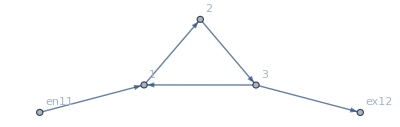

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j115→0,j116→0,j117→0,j118→10,j119→10,j120→0,j121→0,j122→10,j123→0,j124→0,jt125→0,jt126→0,jt127→0,jt128→0,jt129→0,jt130→10,jt131→0,jt132→0,jt133→0,jt134→0,jt135→0,jt136→10,jt137→0,jt138→0,u139→15,u140→5,u141→5,u142→5,u143→15,u144→15,u145→5,u146→15,u147→5,u148→15|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j151→0,j152→0,j153→0,j154→10,j155→10,j156→0,j157→0,j158→10,j159→0,j160→0,jt161→0,jt162→0,jt163→0,jt164→0,jt165→0,jt166→10,jt167→0,jt168→0,jt169→0,jt170→0,jt171→0,jt172→10,jt173→0,jt174→0,u175→7.71442,u176→5.,u177→5.,u178→5,u179→7.71442,u180→7.71442,u181→5.,u182→7.71442,u183→5,u184→7.71442|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j151→0,j152→0,j153→0,j154→10,j155→10,j156→0,j157→0,j158→10,j159→0,j160→0,jt161→0,jt162→0,jt163→0,jt164→0,jt165→0,jt166→10,jt167→0,jt168→0,jt169→0,jt170→0,jt171→0,jt172→10,jt173→0,jt174→0,u175→7.96984,u176→5.,u177→5.,u178→5,u179→7.96984,u180→7.96984,u181→5.,u182→7.96984,u183→5,u184→7.96984|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.9681×10^-17

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 6.9681×10^-17

<|j115→0,j116→0,j117→0,j118→10,j119→10,j120→0,j121→0,j122→10,j123→0,j124→0,jt125→0,jt126→0,jt127→0,jt128→0,jt129→0,jt130→10,jt131→0,jt132→0,jt133→0,jt134→0,jt135→0,jt136→10,jt137→0,jt138→0,u139→8.62682,u140→5.,u141→5.,u142→5,u143→8.62682,u144→8.62682,u145→5.,u146→8.62682,u147→5,u148→8.62682|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j151→0,j152→0,j153→0,j154→10,j155→10,j156→0,j157→0,j158→10,j159→0,j160→0,jt161→0,jt162→0,jt163→0,jt164→0,jt165→0,jt166→10,jt167→0,jt168→0,jt169→0,jt170→0,jt171→0,jt172→10,jt173→0,jt174→0,u175→13.3004,u176→5.,u177→5.,u178→5,u179→13.3004,u180→13.3004,u181→5.,u182→13.3004,u183→5,u184→13.3004|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.06581×10^-14,ComplexInfinity]

<|j151→0,j152→0,j153→0,j154→10,j155→10,j156→0,j157→0,j158→10,j159→0,j160→0,jt161→0,jt162→0,jt163→0,jt164→0,jt165→0,jt166→10,jt167→0,jt168→0,jt169→0,jt170→0,jt171→0,jt172→10,jt173→0,jt174→0,u175→15,u176→5,u177→5,u178→5,u179→15,u180→15,u181→5,u182→15,u183→5,u184→15|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],1,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j151→0,j152→0,j153→0,j154→10,j155→10,j156→0,j157→0,j158→10,j159→0,j160→0,jt161→0,jt162→0,jt163→0,jt164→0,jt165→0,jt166→10,jt167→0,jt168→0,jt169→0,jt170→0,jt171→0,jt172→10,jt173→0,jt174→0,u175→87.1921,u176→5.,u177→5.,u178→5,u179→87.1921,u180→87.1921,u181→5.,u182→87.1921,u183→5,u184→87.1921|>

```mathematica
alpha = 1.77;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.890369

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.963772

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00707

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00001

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«3 more identical outputs»

<|j151→0,j152→0,j153→0,j154→10,j155→10,j156→1.41033×10^214,j157→1.41033×10^214,j158→1.41033×10^214,j159→0,j160→0,jt161→1.41033×10^214,jt162→0,jt163→0,jt164→0,jt165→0,jt166→10,jt167→0,jt168→1.41033×10^214,jt169→0,jt170→0,jt171→1.41033×10^214,jt172→10,jt173→0,jt174→0,u175→0,u176→0.,u177→5.,u178→5,u179→0.,u180→0.,u181→5.,u182→0.,u183→5,u184→0.|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],4,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.10339

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00229

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

<|j151→0,j152→0,j153→0,j154→10,j155→10,j156→6.43959×10^10,j157→6.43959×10^10,j158→6.43959×10^10,j159→0,j160→0,jt161→6.43959×10^10,jt162→0,jt163→0,jt164→0,jt165→0,jt166→10,jt167→0,jt168→6.43959×10^10,jt169→0,jt170→0,jt171→6.43959×10^10,jt172→10,jt173→0,jt174→0,u175→1.9158×10^7,u176→9.57898×10^6,u177→5.,u178→5,u179→1.9158×10^7,u180→9.57898×10^6,u181→5.,u182→1.9158×10^7,u183→5,u184→1.9158×10^7|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00359

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«3 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[-1.42247815737932×10^354-1. j151+1. j156-IntM[-10+j151-j156]]^2+Abs[-1.42247815737932×10^354-1. j151+1. j156-IntM[j151-j156]]^2+Abs[-1.42247815737932×10^354-1. j151+1. j156+0. u175-IntM[j151-j156]]^2),(√(Abs[-1.42247815737932×10^354-1. j151+1. j156-IntM[-10+j151-j156]]^2+Abs[-1.42247815737932×10^354-1. j151+1. j156-IntM[j151-j156]]^2+Abs[-1.42247815737932×10^354-1. j151+1. j156+0. u175-IntM[j151-j156]]^2))/(√(2 Abs[-1.42247815737932×10^354+0. j151+0. j156]^2+Abs[-1.42247815737932×10^354+0. j151+0. j156+0. u175]^2)),(√(Abs[-1.42247815737932×10^354-1. j151+1. j156-IntM[-10+j151-j156]]^2+Abs[-1.42247815737932×10^354-1. j151+1. j156-IntM[j151-j156]]^2+Abs[-1.42247815737932×10^354-1. j151+1. j156+0. u175-IntM[j151-j156]]^2))/(√(Abs[-10+j151-j156+IntM[-10+j151-j156]]^2+2 Abs[j151-j156+IntM[j151-j156]]^2))]

ReplaceAll::reps: {u177==5&&u179==u182&&u181==5&&j151-j156-u175+u180==j151-j156+IntM[j151-j156]&&j151-j156-u176+u181==j151-j156+IntM[j151-j156]&&-10+j151-j156-u177+u182==-10+j151-j156+IntM[-10+j151-j156]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

AssociateTo::invlb: The argument u177==5&&u179==u182&&u181==5&&j151-j156-u175+u180==j151-j156+IntM[j151-j156]&&j151-j156-u176+u181==j151-j156+IntM[j151-j156]&&-10+j151-j156-u177+u182==-10+j151-j156+IntM[-10+j151-j156] is not a list, Rule, or Association.

ReplaceAll::reps: {u177==5&&u179==u182&&u181==5&&j151-j156-u175+u180==j151-j156+IntM[j151-j156]&&j151-j156-u176+u181==j151-j156+IntM[j151-j156]&&-10+j151-j156-u177+u182==-10+j151-j156+IntM[-10+j151-j156]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],8,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00012

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00012

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[1.,ComplexInfinity]

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00012

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

<|j151→0,j152→0,j153→0,j154→10,j155→10,j156→1.10266×10^6,j157→1.10266×10^6,j158→1.10267×10^6,j159→0,j160→0,jt161→1.10266×10^6,jt162→0,jt163→0,jt164→0,jt165→0,jt166→10,jt167→0,jt168→1.10266×10^6,jt169→0,jt170→0,jt171→1.10266×10^6,jt172→10,jt173→0,jt174→0,u175→164783.,u176→82393.9,u177→5.,u178→5,u179→164783.,u180→82393.9,u181→5.,u182→164783.,u183→5,u184→164783.|>